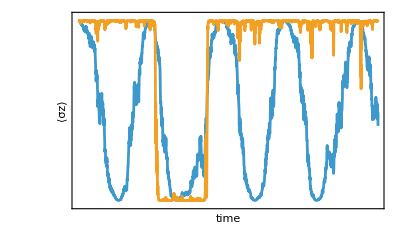

```mathematica
im1=ListLinePlot[{Transpose[{clockZeno, zOf@gentle["states"]}], Transpose[{clockZeno, zOf@hard["states"]}]},
  Frame -> True, GridLines -> Automatic,
PlotRange -> {-1.05, 1.05},
  FrameLabel -> {"time", "⟨σz⟩"},PlotTheme->"Minimal"]
```

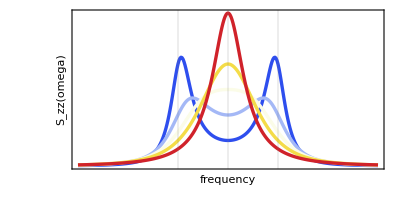

```mathematica
im2=ListLinePlot[Table[Transpose[{tonesQpc, qpcSpectrum[4 OmQpc r, tonesQpc]}], {r, ratioSweep}],
 PlotStyle -> (Directive[#, Thickness[0.006]] & /@ sweepCols),
 Frame -> True, GridLines -> {{-OmQpc, 0, OmQpc}, None}, PlotRange -> All, AspectRatio -> 1/2,
 FrameLabel -> {"frequency", "S_zz(omega)"},
 PlotTheme->"Minimal"]
```

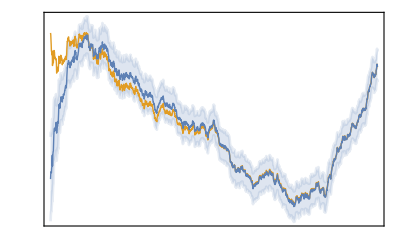

```mathematica
im3=Show[
  ListLinePlot[{Transpose[{kalGrid, kalFilt[[All, 1]] + kalBand}], Transpose[{kalGrid, kalFilt[[All, 1]] - kalBand}]},PlotTheme->"Minimal",
   Filling -> {1 -> {2}}, PlotStyle -> Directive[ColorData[97, 1], Opacity[0.15]]],
  ListLinePlot[{Transpose[{kalGrid, kalTrue[[All, 1]]}], Transpose[{kalGrid, kalFilt[[All, 1]]}]},PlotTheme->"Minimal",
   PlotStyle -> {Directive[Thick, ColorData[97, 2]], Directive[Thick, ColorData[97, 1]]}],
  Frame -> True, GridLines -> Automatic, PlotRange -> All,PlotTheme->"Minimal"]
```

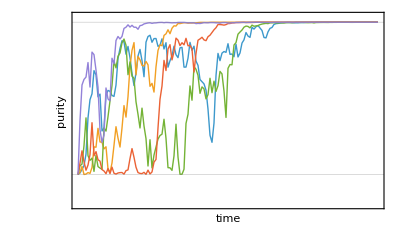

```mathematica
im4=ListLinePlot[Transpose[{0.01 Range[0, Length[#] - 1], #}] & /@ purities,
 Frame -> True, FrameLabel -> {"time", "purity"}, PlotRange -> {Automatic, {0.4, 1.02}},
 GridLines -> {None, {0.5, 1.}}, PlotStyle -> Thick,
 PlotTheme->"Minimal"]
```

```mathematica
im5=blochPlot[{blochVector /@ watchedAll["states"], blochVector /@ watchedOne["states"]}]
```

-Graphics3D-

```mathematica
im6=With[{gg = 1., om = 3.},
 Module[{startsFlat, startsOrtho, path},
  startsFlat = N[flatPair /. {γ -> gg, Ω -> om}];
  startsOrtho = N[orthPair /. {γ -> gg, Ω -> om}];
  path[r0_] := With[{run = evolveODE[(om/2) X, {Sqrt[gg] lower}, r0, 14.]},
    blochVector[run[#]] & /@ Range[0, 14, 0.02]];
  blochPlot[{path[densityMatrix[{Cos[π/8], E^(I π/4) Sin[π/8]}]], path[blochState @@ startsFlat[[1]]],
    path[blochState @@ startsFlat[[2]]], path[blochState @@ startsOrtho[[1]]],
    path[blochState @@ startsOrtho[[2]]]}   ]]]
```

-Graphics3D-

```mathematica
ImageCollage[{1,1,1,1,.5,.5}->{im1,im2,im3,im4,im5,im6},Background->None]
```

-Graphics-

```mathematica
GraphicsRow@{im1,im2,im3,im4,im5,im6}
```

-Graphics-

```mathematica
GraphicsGrid[{{im5,im2,im3},{im4,im1,im6}},Background->White]
```

-Graphics-